```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

### Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,len_]:=Module[{temp=Range[1,len],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,len}];output=temp;];

store[param_,res_,model_,temp_]:=Module[{name=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tmuscan/results/"<>name<>"T"<>ToString[temp]<>".dat",res];];

storearea[res_,model_,temp_]:=Module[{name=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])(const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tmuscan/results/"<>name<>"T"<>ToString[temp]<>".dat",res];];

import[res_,temp_]:=res=Import["spectraldata/Tmuscan/results/"<>ToString[res]<>"T"<>ToString[temp]<>".dat"];
```

## Critical Temperature 155MeV

```mathematica
Tmuscan=Join[Table[{0.145,i},{i,0.,0.155,0.005}],Table[{0.145,i},{i,0.16,1.,0.05}]]
```

{{0.145,0.},{0.145,0.005},{0.145,0.01},{0.145,0.015},{0.145,0.02},{0.145,0.025},{0.145,0.03},{0.145,0.035},{0.145,0.04},{0.145,0.045},{0.145,0.05},{0.145,0.055},{0.145,0.06},{0.145,0.065},{0.145,0.07},{0.145,0.075},{0.145,0.08},{0.145,0.085},{0.145,0.09},{0.145,0.095},{0.145,0.1},{0.145,0.105},{0.145,0.11},{0.145,0.115},{0.145,0.12},{0.145,0.125},{0.145,0.13},{0.145,0.135},{0.145,0.14},{0.145,0.145},{0.145,0.15},{0.145,0.155},{0.145,0.16},{0.145,0.21},{0.145,0.26},{0.145,0.31},{0.145,0.36},{0.145,0.41},{0.145,0.46},{0.145,0.51},{0.145,0.56},{0.145,0.61},{0.145,0.66},{0.145,0.71},{0.145,0.76},{0.145,0.81},{0.145,0.86},{0.145,0.91},{0.145,0.96}}

```mathematica
Do[ccdata[n]=Import["spectraldata/Tmuscan/cc/swccT"<>ToString[Round[1000 Tmuscan[[n,1]]]]<>"mu"<>ToString[Round[1000 Tmuscan[[n,2]]]]<>"spectra.dat"];,{n,Length[Tmuscan]}];
Do[ccdatau[n]=Import["spectraldata/Tmuscan/cc/swccT"<>ToString[Round[1000 Tmuscan[[n,1]]]]<>"mu"<>ToString[Round [1000 Tmuscan[[n,2]]]]<>"uspectra.dat"];,{n,Length[Tmuscan]}];
Do[ccdatal[n]=Import["spectraldata/Tmuscan/cc/swccT"<>ToString[Round[1000 Tmuscan[[n,1]]]]<>"mu"<>ToString[Round[1000 Tmuscan[[n,2]]]]<>"lspectra.dat"];,{n,Length[Tmuscan]}];
```

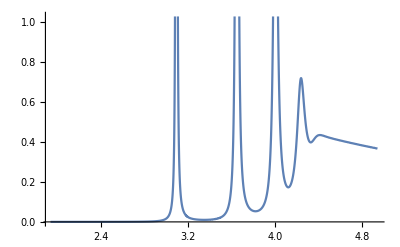

```mathematica
ListPlot[ccdatal[1],Joined->True]
```

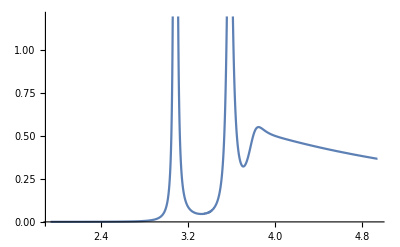

```mathematica
ListPlot[ccdata[1],Joined->True]
```

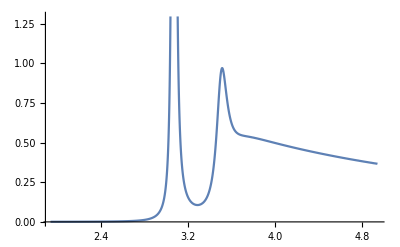

```mathematica
ListPlot[ccdatau[1],Joined->True]
```

### Perform Fitting

```mathematica
Clear[ccmodel,ccmodell,ccmodelu]
fitnew[ccdata,ccmodel,Length[Tmuscan]];
fitnew[ccdatau,ccmodelu,Length[Tmuscan]];
fitnew[ccdatal,ccmodell,Length[Tmuscan]];
```

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];,{i,Length[ccmodel]}];
Do[If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];,{i,Length[ccmodelu]}];
Do[If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodell]}];
```

```mathematica
Clear[wrfitcc,gfitcc,areafitcc,cfitcc,dfitcc,sfitcc,s2fitcc,wrfitccu,gfitccu,areafitccu,cfitccu,dfitccu,sfitccu,s2fitccu,wrfitccl,gfitccl,areafitccl,cfitccl,dfitccl,sfitccl,s2fitccl];
```

```mathematica
T=Round[1000 Tmuscan[[1,1]]];
```

```mathematica
store[wr,wrfitcc,ccmodel,T];
store[Γ,gfitcc,ccmodel,T];
store[const,cfitcc,ccmodel,T];
store[δbg,dfitcc,ccmodel,T];
store[shift,sfitcc,ccmodel,T];
store[shift2,s2fitcc,ccmodel,T];
storearea[areafitcc,ccmodel,T];
store[wr,wrfitccu,ccmodelu,T];
store[Γ,gfitccu,ccmodelu,T];
store[const,cfitccu,ccmodelu,T];
store[δbg,dfitccu,ccmodelu,T];
store[shift,sfitccu,ccmodelu,T];
store[shift2,s2fitccu,ccmodelu,T];
storearea[areafitccu,ccmodelu,T];
store[wr,wrfitccl,ccmodell,T];
store[Γ,gfitccl,ccmodell,T];
store[const,cfitccl,ccmodell,T];
store[δbg,dfitccl,ccmodell,T];
store[shift,sfitccl,ccmodell,T];
store[shift2,s2fitccl,ccmodell,T];
storearea[areafitccl,ccmodell,T];
```

### Import previous results

```mathematica
import[wrfitcc,T];
import[gfitcc,T];
import[cfitcc,T];
import[dfitcc,T];
import[sfitcc,T];
import[s2fitcc,T];
import[areafitcc,T];
import[wrfitccu,T];
import[gfitccu,T];
import[cfitccu,T];
import[dfitccu,T];
import[sfitccu,T];
import[s2fitccu,T];
import[areafitccu,T];
import[wrfitccl,T];
import[gfitccl,T];
import[cfitccl,T];
import[dfitccl,T];
import[sfitccl,T];
import[s2fitccl,T];
import[areafitccl,T];
```

### View results

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitcc],1},{ii,1,Length[wrfitcc[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccu],1},{ii,1,Length[wrfitccu[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccl],1},{ii,1,Length[wrfitccl[[1]]],1}]
```

### Dilepton ratio

```mathematica
Emfactor=2.356305815440891;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0=ConstantArray[0,Length[wrfitcc]];
Do[If[Length[wrfitcc[[ii]]]==2,R0[[ii]]={Tmuscan[[ii,2]],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tmuscan[[ii,1]]])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tmuscan[[ii,1]]])}],{ii,Length[R0]}];
R0u=ConstantArray[0,Length[wrfitccu]];
Do[If[Length[wrfitccu[[ii]]]==2,R0u[[ii]]={Tmuscan[[ii,2]],Emfactor (areafitccu[[ii,2]]nB[wrfitccu[[ii,2]],Tmuscan[[ii,1]]])/(areafitccu[[ii,1]]nB[wrfitccu[[ii,1]],Tmuscan[[ii,1]]])}],{ii,Length[R0u]}];
R0l=ConstantArray[0,Length[wrfitccl]];
Do[If[Length[wrfitccl[[ii]]]==2,R0l[[ii]]={Tmuscan[[ii,2]],Emfactor (areafitccl[[ii,2]]nB[wrfitccl[[ii,2]],Tmuscan[[ii,1]]])/(areafitccl[[ii,1]]nB[wrfitccl[[ii,1]],Tmuscan[[ii,1]]])}],{ii,Length[R0l]}];
```

```mathematica
R0=DeleteCases[R0,0];
R0u=DeleteCases[R0u,0];
R0l=DeleteCases[R0l,0];
```

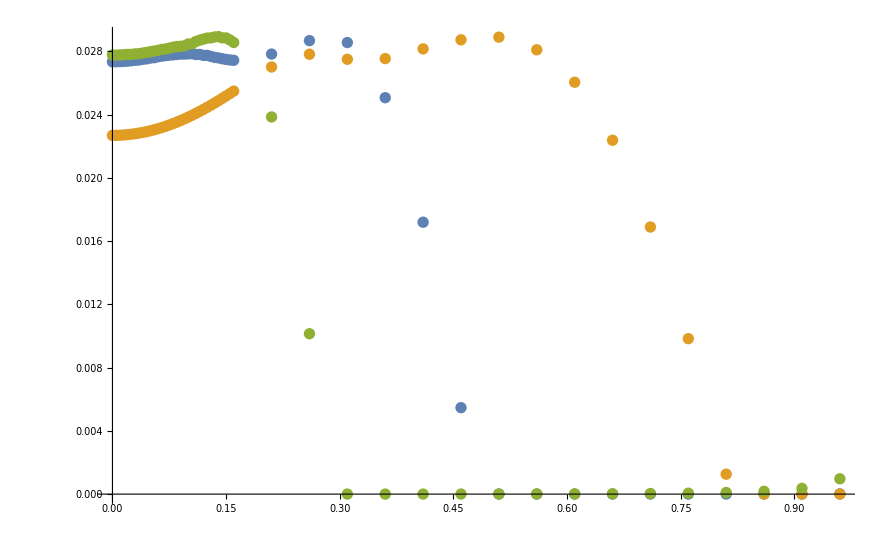

```mathematica
ListPlot[{R0,R0l,R0u}]
```

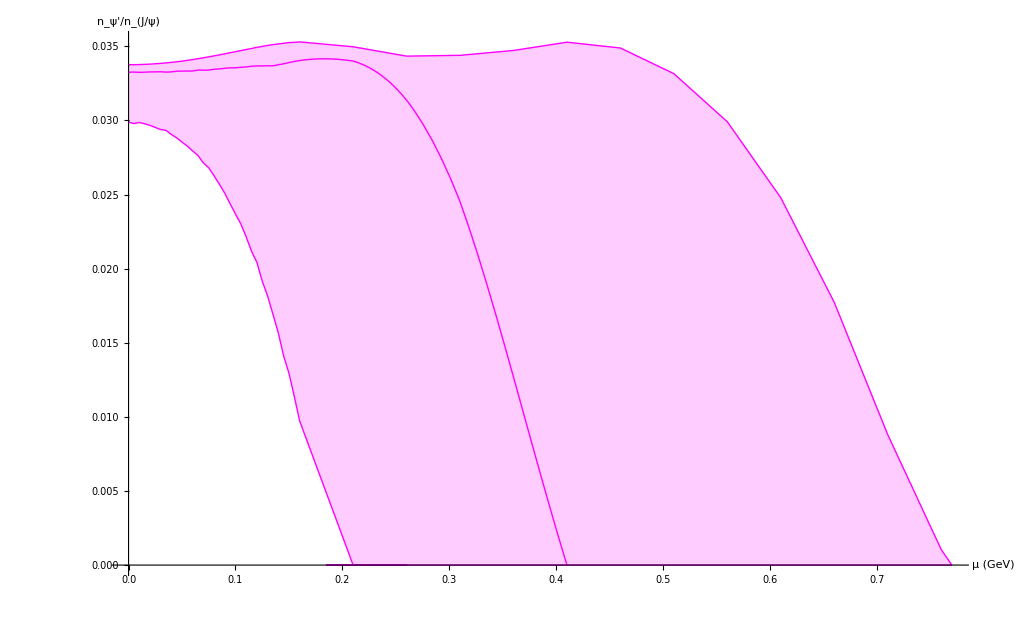

```mathematica
Show[{ListPlot[{Append[R0l[[;;-5]]/.{x_,y_}:>{x,y+2(R0[[1,2]]-R0l[[1,2]])},{0.77,0}],Append[Append[R0u[[;;-15]],{0.185,0.}],{0.77,0.}]},PlotRange->All,Joined->True,PlotStyle->{{Magenta,Thin},{Magenta,Thin}},Filling->{1->{2}},FillingStyle->Opacity[0.2],AxesLabel->{Style["μ (GeV)",20,Black],Style["n_ψ'/n_(J/ψ)",20,Black]},AxesStyle->{{Black,20},{Black,20}}],Plot[Interpolation[R0[[;;-12]]][x],{x,0,0.41},PlotStyle->{Magenta,Thick}]}]
```

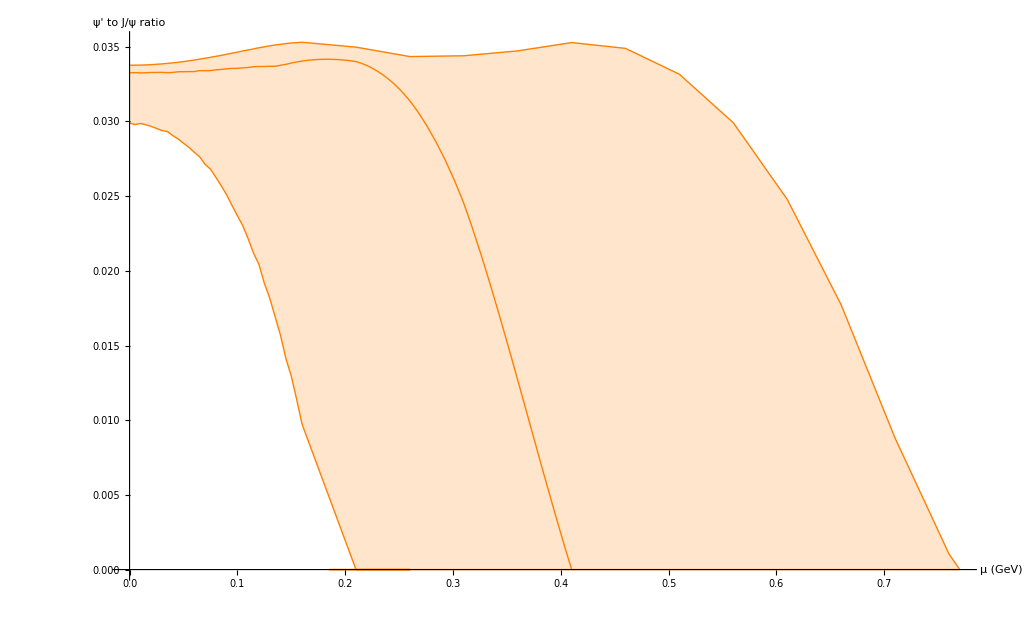

```mathematica
Show[%55,AxesStyle->Black]
```

```mathematica
Plot[2 Sin[x],{x,0,10},AxesLabel->{x,2 Sin[x]},LabelStyle->Directive[Blue,Bold]]
```

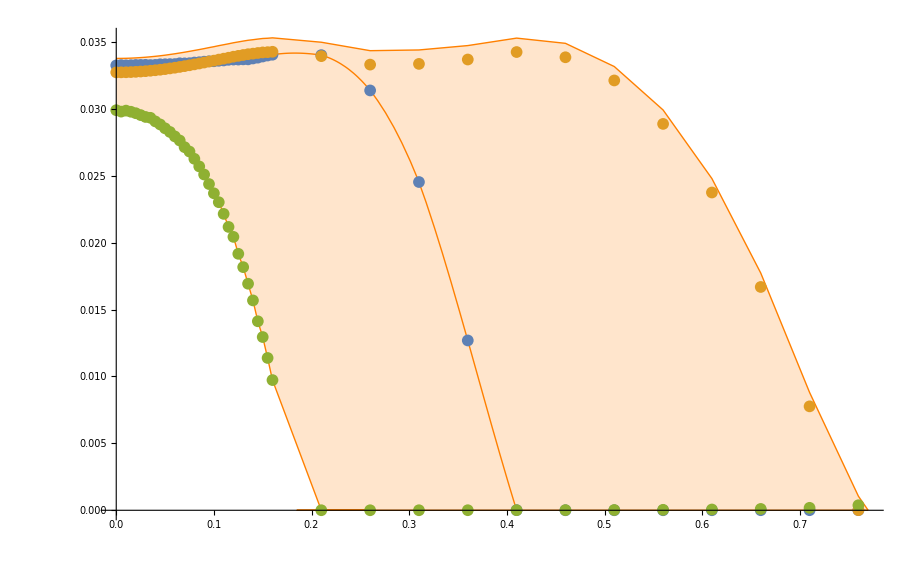

```mathematica
Show[ListPlot[{Append[R0l[[;;-5]]/.{x_,y_}:>{x,y+2(R0[[1,2]]-R0l[[1,2]])},{0.77,0}],Append[Append[R0u[[;;-15]],{0.185,0.}],{0.77,0.}]},PlotRange->All,Joined->True,PlotStyle->{{Orange,Thin},{Orange,Thin}},Filling->{1->{2}},FillingStyle->Opacity[0.2]],Plot[Interpolation[R0[[;;-12]]][x],{x,0,0.41},PlotStyle->{Orange,Thick}],ListPlot[{R0,R0l,R0u}]]
```